```mathematica
CountGood2[13]
```

{13,294875,2615819}

```mathematica
CountGood2[14]
```

$Aborted

```mathematica
vals={{5,0,0},{6,5,6},{7,35,59},{8,185,426},{9,875,2699},{10,3905,15906},{11,16835,89579},{12,70985,489306},{13,294875,2615819}};
```

```mathematica
Map[#[[2]]/StirlingS2[#[[1]],4]&,vals]
```

{0,1/13,1/10,185/1701,25/222,781/6821,3367/29150,70985/611501,8425/72358}

```mathematica
N[Map[#[[2]]/StirlingS2[#[[1]],4]&,vals]]
```

{0.,0.0769231,0.1,0.10876,0.112613,0.114499,0.115506,0.116083,0.116435}

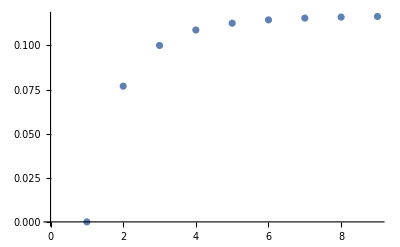

```mathematica
Map[#[[2]]/StirlingS2[#[[1]],4]&,vals]//ListPlot
```

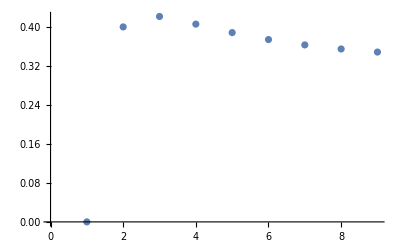

```mathematica
Map[#[[3]]/StirlingS2[#[[1]],5]&,vals]//ListPlot
```